# 计算物理范例

### 方程组的求解

```mathematica
Solve[x1+2x2+x3==0&&2x1+2x2+3x3==3&&-x1-3x2==0,{x1,x2,x3}]
```

{{x1→9,x2→-3,x3→-3}}

```mathematica
NSolve[x^2-10x+y^2+4==0&&x y^2+x-10y+4==0,{x,y},Reals]
```

{{x→2.25893,y→3.6724},{x→0.439871,y→0.453014}}

### 函数近似

InterpolatingFunction[…]

FittedModel[Sin[1.00025 x]]

Sin[1.00025 x]

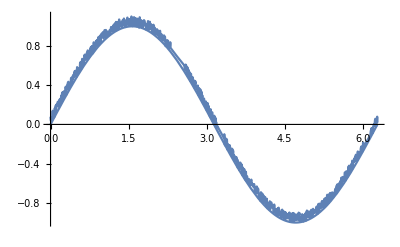

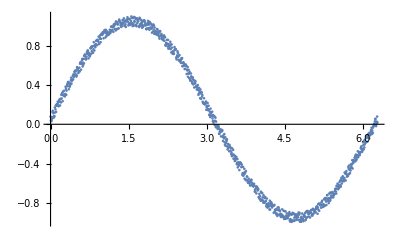

```mathematica
data = {Range[0,2Pi,2Pi/999],Sin[Range[0,2Pi,2Pi/999]]+RandomReal[{0,0.1},1000]};
interpf=Interpolation[Transpose[data]]
nol=NonlinearModelFit[Transpose[data],Sin[a*x],{a},{x}]
Normal[nol]
Show[Plot[interpf[x],{x,0,2Pi}],Plot[nol[x],{x,0,2Pi}]]
ListPlot[Transpose[data]]
```

### 导数的运算

```mathematica
f[x_,y_]:=(x^2+4 y^2-9)^2+(18y-14 x^2+45)^2
D[f[x,y],{{x,y}}]//Simplify
Series[1/(Cos[θ]-a),{θ,0,4}]
```

{4 x (-639+197 x^2-252 y+4 y^2),1620+504 y+64 y^3+8 x^2 (-63+2 y)}

1/(1-a)+θ^2/(2 (-1+a)^2)+((-5-a) θ^4)/(24 (-1+a)^3)+O[θ]^5

```mathematica
Integrate[Sin[x]*Cos[y],x,y]
```

-Cos[x] Sin[y]

```mathematica
Integrate[x^p(1-x)^q,{x,0,1},Reals]
```

ConditionalExpression[(ℝ Gamma[1+p] Gamma[1+q])/Gamma[2+p+q],Re[p]>-1&&Re[q]>-1]

### 求解微分方程(组）

```mathematica
DSolve[{y''[x]+9.8+0.01*y'[x]==0,y[0]==0,y[5]==40},y,x]
y'[x]/.%/.x->0
```

{{y→({x}↦-980. ⅇ^(-0.01 x) (1. ⅇ^(0.01 x) x-103.358 ⅇ^(0.01 x)+103.358))}}

{32.9058}

```mathematica
sol=NDSolve[{x''[t]==x[t]-y[t]-(3*x'[t])^2+(y'[t])^3+6*y''[t]+2t,y'''[t]==y''[t]-x'[t]+ⅇ^x[t]-t,x[1]==2,x'[1]==-4,y[1]==-2,y'[1]==7,y''[1]==6},{x,y},{t,1,1.6}]
Plot[{x[t]/.sol,y[t]/.sol},{t,1,1.6}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

```mathematica
DSolve[{u''[t]==-Pi^2(u[t]+1)/4,u[0]==0,u[1]==1},u,t]
```

{{u→Function[{t},-1+Cos[(π t)/2]+2 Sin[(π t)/2]]}}

### 求解偏微分方程

```mathematica
DSolve[{u''[x]==β^2 u[x]^2,u[Infinity]==0,u'[Infinity]==0},u,x]
```

Infinity::indet: 碰到不定表达式 -∞+∞.

Table::iterb: 迭代器 {x,∞,∞,0.1} 没有适当的边界.

Table::nliter: 位置 2 处的非列表迭代器(non-list iterator) Quiet[PossibleZeroQ[Chop[DSolve`DSolveExtendedLibraryDump`check1]]] 没有算出实数值.

Infinity::indet: 碰到不定表达式 -∞+∞.

Table::iterb: 迭代器 {x,∞,∞,0.1} 没有适当的边界.

Table::nliter: 位置 2 处的非列表迭代器(non-list iterator) Quiet[PossibleZeroQ[Chop[DSolve`DSolveExtendedLibraryDump`check1]]] 没有算出实数值.

DSolve::bvlim: 对于通解的某些分支，无法计算给定点的极限. 某些解可能会丢失.

{}